```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
controlColor=Black;
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
dateMouseListControl={{"011622","Mouse22550"},{"011822","Mouse22550"},{"012322","Mouse22549"},{"012622","Mouse22549"},{"021022","Mouse22549"},{"010522","Mouse22599"},{"021022","Mouse22599"},{"021422","Mouse22599"},{"033122","Mouse22544"},{"040122","Mouse22562"},{"040322","Mouse22544"},{"040322","Mouse22562"}};
```

```mathematica
dateMouseListV1axons={{"112221","Mouse22485"},{"112321","Mouse22485"},{"120321","Mouse22485"},{"120821","Mouse22517"},{"121321","Mouse22485"},{"010122","Mouse22547"},{"011222","Mouse22501"},{"011622","Mouse22504"},{"011822","Mouse22504"},{"012322","Mouse22575"},{"012722","Mouse22575"},{"013122","Mouse22504"},{"021022","Mouse22504"},{"021222","Mouse22575"},{"032222","Mouse22506"},{"032622","Mouse22506"},{"040422","Mouse22506"}};
```

```mathematica
dateMouseListLPaxons={{"020122","Mouse22413"},{"020922","Mouse22413"},{"021422","Mouse22413"},{"012622","Mouse22514"},{"012822","Mouse22514"},{"020122","Mouse22514"},{"021122","Mouse22519"},{"021122","Mouse22535"},{"021522","Mouse22535"},{"021722","Mouse22519"},{"030122","Mouse22513"},{"030222","Mouse22521"},{"030722","Mouse22513"},{"030822","Mouse22521"},{"030822","Mouse22519"},{"031522","Mouse22513"},{"031522","Mouse22521"},{"031922","Mouse22521"},{"032022","Mouse22519"},{"032222","Mouse22513"},{"040622","Mouse22513"}};
```

```mathematica
dateMouseListLMaxons={{"022022","Mouse22563"},{"022222","Mouse22563"},{"031722","Mouse22539"},{"031722","Mouse22570"},{"032022","Mouse22539"},{"032022","Mouse22570"},{"032322","Mouse22539"},{"032522","Mouse22539"},{"041022","Mouse22407"},{"041522","Mouse22407"}};
```

```mathematica
(****************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 5E****************) 
(**********************************************)
```

```mathematica
pairedROIsControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(***Import CRFs for all paired ROIs to compute global response averages***)
```

```mathematica
(*****)
```

```mathematica
allResponsesBeforeControl=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/Session1","/VisStimResults/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_Session1","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsControl[[n]]}],{n,1,Length[dateMouseListControl]}]];
```

```mathematica
allResponsesAfterControl=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/Session2","/VisStimResults/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_Session2","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsControl[[n]]}],{n,1,Length[dateMouseListControl]}]];
```

```mathematica
pairedRespControl=Partition[Riffle[allResponsesBeforeControl,allResponsesAfterControl],2];
```

```mathematica
maxValControl=4;
```

```mathematica
minValControl=0;
```

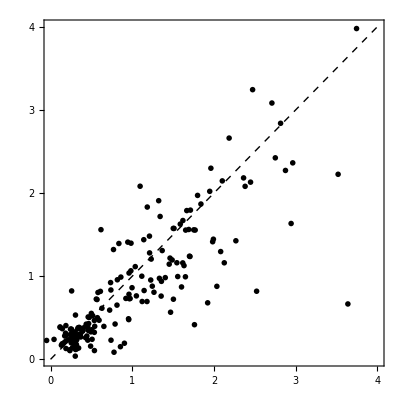

```mathematica
Show[ListPlot[pairedRespControl,PlotRange->{{minValControl,maxValControl},{minValControl,maxValControl}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{controlColor,PointSize[0.01]},FrameTicks->{{LinTicks[minValControl,maxValControl,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minValControl,maxValControl,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,minValControl,maxValControl},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
diffsControl=Table[(pairedRespControl[[n,2]]-pairedRespControl[[n,1]]),{n,1,Length[pairedRespControl]}];
```

```mathematica
(*****)
```

```mathematica
allResponsesBeforeV1axons=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/Session1","/VisStimResults/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_Session1","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}]];
```

```mathematica
allResponsesAfterV1axons=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/Session2","/VisStimResults/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_Session2","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}]];
```

```mathematica
pairedRespV1axons=Partition[Riffle[allResponsesBeforeV1axons,allResponsesAfterV1axons],2];
```

```mathematica
maxValV1axons=4;
```

```mathematica
minValV1axons=0;
```

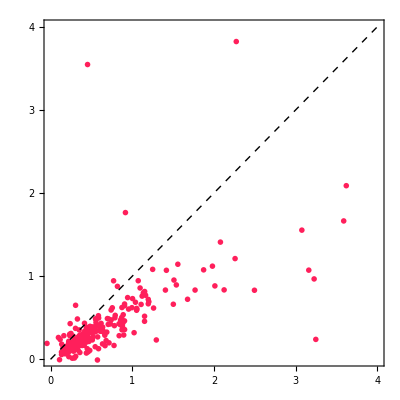

```mathematica
Show[ListPlot[pairedRespV1axons,PlotRange->{{minValV1axons,maxValV1axons},{minValV1axons,maxValV1axons}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{v1Color,PointSize[0.01]},FrameTicks->{{LinTicks[minValV1axons,maxValV1axons,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minValV1axons,maxValV1axons,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,minValV1axons,maxValV1axons},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
diffsV1axons=Table[(pairedRespV1axons[[n,2]]-pairedRespV1axons[[n,1]]),{n,1,Length[pairedRespV1axons]}];
```

```mathematica
(*****)
```

```mathematica
allResponsesBeforeLPaxons=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/Session1","/VisStimResults/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_Session1","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}]];
```

```mathematica
allResponsesAfterLPaxons=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/Session2","/VisStimResults/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_Session2","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}]];
```

```mathematica
pairedRespLPaxons=Partition[Riffle[allResponsesBeforeLPaxons,allResponsesAfterLPaxons],2];
```

```mathematica
maxValLPaxons=4;
```

```mathematica
minValLPaxons=0;
```

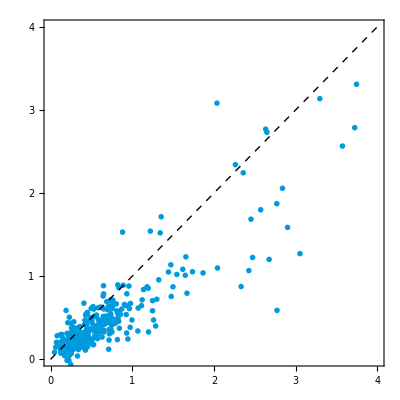

```mathematica
Show[ListPlot[pairedRespLPaxons,PlotRange->{{minValLPaxons,maxValLPaxons},{minValLPaxons,maxValLPaxons}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lpColor,PointSize[0.01]},FrameTicks->{{LinTicks[minValLPaxons,maxValLPaxons,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minValLPaxons,maxValLPaxons,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,minValLPaxons,maxValLPaxons},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
diffsLPaxons=Table[(pairedRespLPaxons[[n,2]]-pairedRespLPaxons[[n,1]]),{n,1,Length[pairedRespLPaxons]}];
```

```mathematica
(*****)
```

```mathematica
allResponsesBeforeLMaxons=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/Session1","/VisStimResults/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_Session1","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}]];
```

```mathematica
allResponsesAfterLMaxons=Flatten[Table[Mean/@Table[(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/Session2","/VisStimResults/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_Session2","_","crf_ROI",ToString[roi],".txt"],"List"])[[All,2]],{roi,pairedROIsLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}]];
```

```mathematica
pairedRespLMaxons=Partition[Riffle[allResponsesBeforeLMaxons,allResponsesAfterLMaxons],2];
```

```mathematica
maxValLMaxons=4;
```

```mathematica
minValLMaxons=0;
```

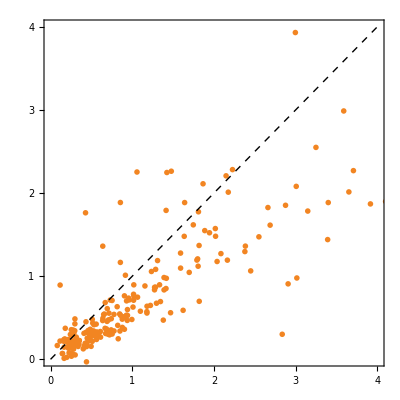

```mathematica
Show[ListPlot[pairedRespLMaxons,PlotRange->{{minValLMaxons,maxValLMaxons},{minValLMaxons,maxValLMaxons}},AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0],PlotStyle->{lmColor,PointSize[0.01]},FrameTicks->{{LinTicks[minValLMaxons,maxValLMaxons,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[minValLMaxons,maxValLMaxons,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}}],Plot[x,{x,minValLMaxons,maxValLMaxons},PlotStyle->{Black,Thick,Dashed}]]
```

```mathematica
diffsLMaxons=Table[(pairedRespLMaxons[[n,2]]-pairedRespLMaxons[[n,1]]),{n,1,Length[pairedRespLMaxons]}];
```

```mathematica
(***********************************************************)
```

```mathematica
(************)
```

```mathematica
bin=2*InterquartileRange[diffsControl]*(Length[diffsControl]^(-1/3))
```

0.134024

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsControl},{-4,4,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{controlColor}),PerformanceGoal->"Speed",PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
h2=Histogram[{diffsControl},{-4,4,bin},hfn,ChartStyle->{{controlColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

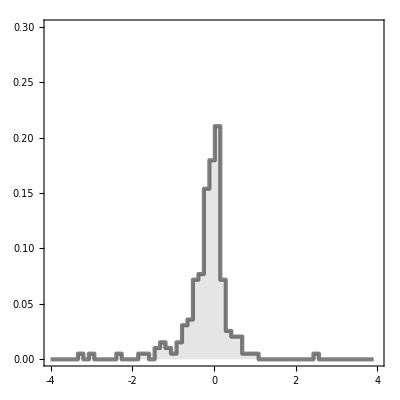

```mathematica
histModIndexControl=Show[hline,h2,PlotRange->{{-4,4},{0,0.3}},FrameTicks->{{LinTicks[0,0.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsV1axons]*(Length[diffsV1axons]^(-1/3));
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsV1axons},{-4,4,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{v1Color}),PerformanceGoal->"Speed",PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
h2=Histogram[{diffsV1axons},{-4,4,bin},hfn,ChartStyle->{{v1Color},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

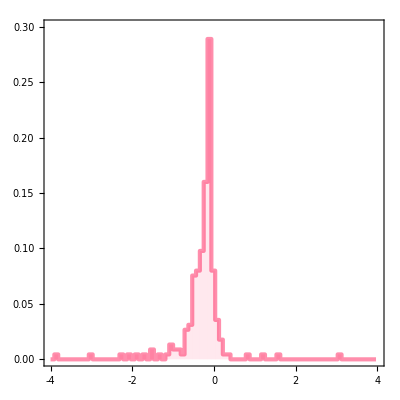

```mathematica
histModIndexV1axons=Show[hline,h2,PlotRange->{{-4,4},{0,0.3}},FrameTicks->{{LinTicks[0,0.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsLPaxons]*(Length[diffsLPaxons]^(-1/3));
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsLPaxons},{-4,4,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lpColor}),PerformanceGoal->"Speed",PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
h2=Histogram[{diffsLPaxons},{-4,4,bin},hfn,ChartStyle->{{lpColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

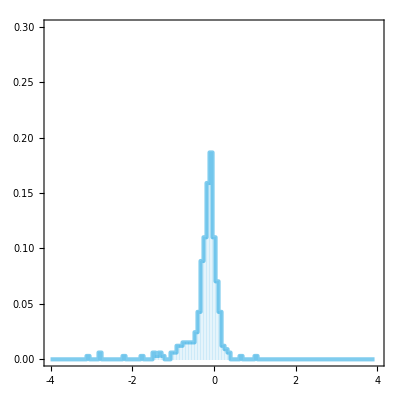

```mathematica
histModIndexLPaxons=Show[hline,h2,PlotRange->{{-4,4},{0,0.3}},FrameTicks->{{LinTicks[0,0.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
bin=2*InterquartileRange[diffsLMaxons]*(Length[diffsLMaxons]^(-1/3));
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{diffsLMaxons},{-4,4,bin},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{lmColor}),PerformanceGoal->"Speed",PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
h2=Histogram[{diffsLMaxons},{-4,4,bin},hfn,ChartStyle->{{lmColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-4,4},{0,0.3}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

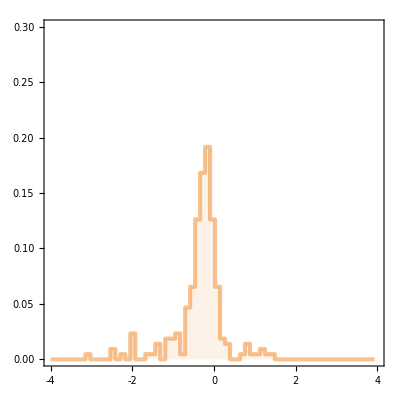

```mathematica
histModIndexLMaxons=Show[hline,h2,PlotRange->{{-4,4},{0,0.3}},FrameTicks->{{LinTicks[0,0.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 5F****************) 
(**********************************************)
```

```mathematica
controlCharts=Show[BoxWhiskerChart[diffsControl,{{"Whiskers", Directive[Darker@controlColor,Thick]}, {"Fences", Directive[Darker@controlColor,Thick]},{"MedianMarker", Directive[Darker@controlColor,Thickness[0.009]]}},PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[controlColor,Opacity[0.3]],Frame->False],DistributionChart[diffsControl,PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],controlColor],Frame->False],FrameTicks->{{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[diffsV1axons,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[diffsV1axons,PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[diffsLMaxons,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[diffsLMaxons,PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[diffsLPaxons,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[diffsLPaxons,PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[diffsControl,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.7,0.7}},ChartStyle->Transparent,Frame->False],DistributionChart[diffsControl,PlotRange->{All,{-0.7,0.7}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.7,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

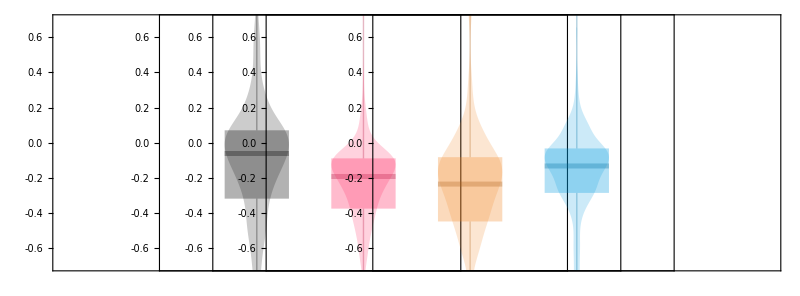

```mathematica
GraphicsRow[{controlCharts,v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```